```mathematica
gpd=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-s-up-xi1-pi-noD.wdx"];
Hdg=Query[1,1]@gpd;
Her=Query[1,2]@gpd;
Hda=Query[1,3]@gpd;
Edg=Query[2,1]@gpd;
Eer=Query[2,2]@gpd;
Eda=Query[2,3]@gpd;
Hdgf=Interpolation[Flatten[Hdg,1]];
Herf=Interpolation[Flatten[Her,1]];
Hdaf=Interpolation[Flatten[Hda,1]];
Edgf=Interpolation[Flatten[Edg,1]];
Eerf=Interpolation[Flatten[Eer,1]];
Edaf=Interpolation[Flatten[Eda,1]];
```

```mathematica
gpdr=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-r-up-xi1-pi-noD.wdx"];
Hdg=Query[1,1]@gpdr;
Her=Query[1,2]@gpdr;
Hda=Query[1,3]@gpdr;
Edg=Query[2,1]@gpdr;
Eer=Query[2,2]@gpdr;
Eda=Query[2,3]@gpdr;
Hdgf=Interpolation[Flatten[Hdg,1]];
Herf=Interpolation[Flatten[Her,1]];

Edgf=Interpolation[Flatten[Edg,1]];
Eerf=Interpolation[Flatten[Eer,1]];
```

```mathematica
Herall[x_,t_]:=Herf[x,t]+Hdaf[x,t];
Eerall[x_,t_]:=Eerf[x,t]+Edaf[x,t];
```

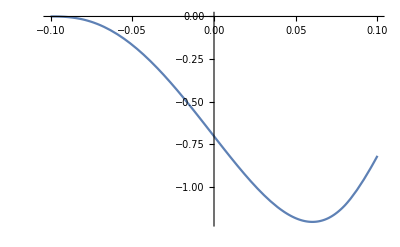

```mathematica
Plot[-I*Herf[x,-1],{x,-0.1,0.1},PlotRange->All]
```

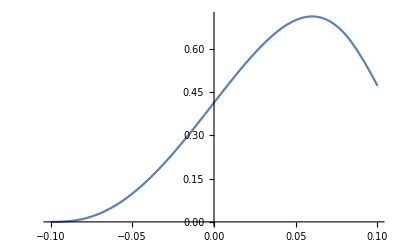

```mathematica
Plot[-I*Eerf[x,-1],{x,-0.1,0.1},PlotRange->All]
```

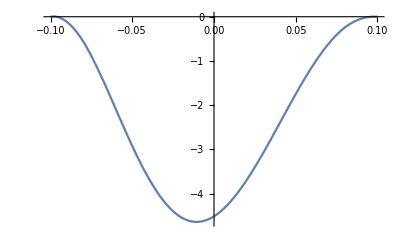

```mathematica
Plot[-I*Hdaf[x,-1],{x,-0.1,0.1},PlotRange->All]
```

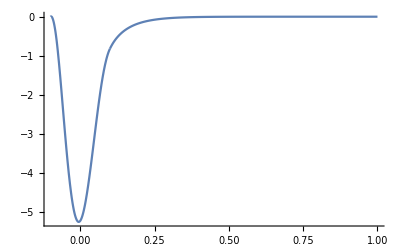

```mathematica
Show[Plot[-I*Hdgf[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Herall[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

```mathematica
Show[Plot3D[-I*Hdgf[x,t],{x,0.1,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[-I*Herall[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","H(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-

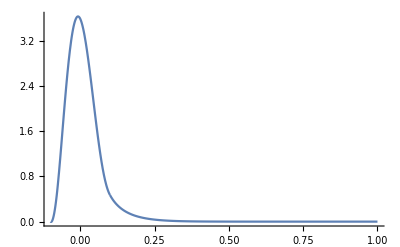

```mathematica
Show[Plot[-I*Edgf[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Eerall[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

```mathematica
Plot[-I*Hdaf[x,-1],{x,-0.1,0.1}]
```

-Graphics-

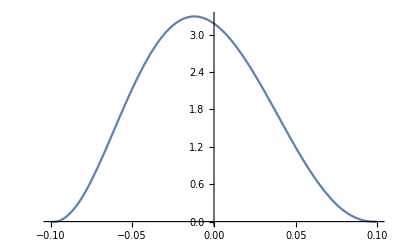

```mathematica
Plot[-I*Edaf[x,-1],{x,-0.1,0.1}]
```

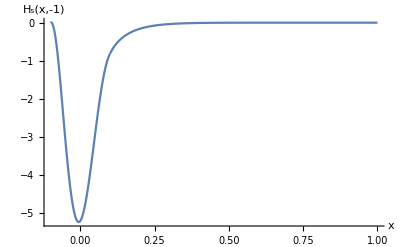

```mathematica
pHs2d=Show[Plot[-I*Hdgf[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Herall[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","H_s(x,-1)"}]
```

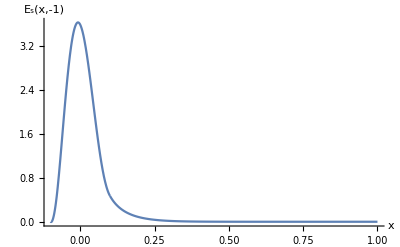

```mathematica
pEs2d=Show[Plot[-I*Edgf[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Eerall[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","E_s(x,-1)"}]
```

```mathematica
pHs3d=Show[Plot3D[-I*Hdgf[x,t],{x,0.1,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[-I*Herall[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","H_s(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-

```mathematica
pEs3d=Show[Plot3D[-I*Edgf[x,t],{x,0.1,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[-I*Eerall[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","E_s(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-

```mathematica
spathH3d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"s-Hu-0.1.pdf"}];
spathH=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"s-Hu-0.1-2d.pdf"}];
```

```mathematica
spathE3d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"s-Eu-0.1.pdf"}];
spathE=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"s-Eu-0.1-2d.pdf"}];
```

```mathematica
Export[spathH3d,pHs3d]
Export[spathH,pHs2d]
```

G:\calc-online\gpd\3dre\228test\s-Hu-0.1.pdf

G:\calc-online\gpd\3dre\228test\s-Hu-0.1-2d.pdf

```mathematica
Export[spathE3d,pEs3d]
Export[spathE,pEs2d]
```

G:\calc-online\gpd\3dre\228test\s-Eu-0.1.pdf

G:\calc-online\gpd\3dre\228test\s-Eu-0.1-2d.pdf

```mathematica
(*下面的是r图*)
```

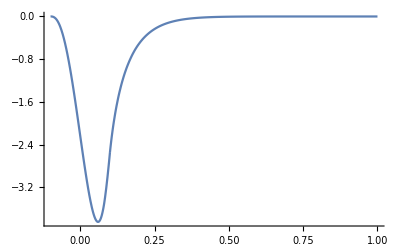

```mathematica
Show[Plot[-I*Hdgf[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Herf[x,-1],{x,-0.1,0.1},PlotRange->All]]
```

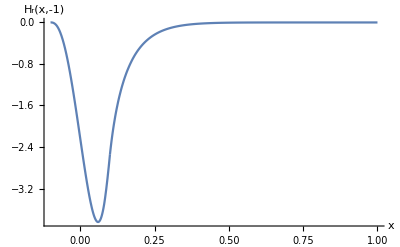

```mathematica
pHr2d=Show[Plot[-I*Hdgf[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Herf[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","H_r(x,-1)"}]
```

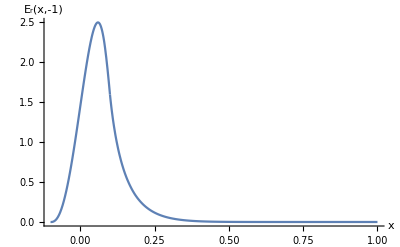

```mathematica
pEr2d=Show[Plot[-I*Edgf[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Eerf[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","E_r(x,-1)"}]
```

```mathematica
pHr3d=Show[Plot3D[-I*Hdgf[x,t],{x,0.1,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[-I*Herf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","H_r(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-

```mathematica
pEr3d=Show[Plot3D[-I*Edgf[x,t],{x,0.1,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[-I*Eerf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","E_r(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-

```mathematica
rpathH3d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"r-Hu-0.1.pdf"}];
rpathH=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"r-Hu-0.1-2d.pdf"}];
```

```mathematica
rpathE3d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"r-Eu-0.1.pdf"}];
rpathE=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"r-Eu-0.1-2d.pdf"}];
```

```mathematica
Export[rpathH3d,pHr3d]
Export[rpathH,pHr2d]
```

G:\calc-online\gpd\3dre\228test\r-Hu-0.1.pdf

G:\calc-online\gpd\3dre\228test\r-Hu-0.1-2d.pdf

```mathematica
Export[rpathE3d,pEr3d]
Export[rpathE,pEr2d]
```

G:\calc-online\gpd\3dre\228test\r-Eu-0.1.pdf

G:\calc-online\gpd\3dre\228test\r-Eu-0.1-2d.pdf